```mathematica
(* FIGURE 6 *)
(* Dib9 energy 20 Kev ? 11/05/11  image by curved crystal, new formula, source fied at distance p , image at distance q , curvature adjusted for chromatic focusing ; R*cos(theta)=2pq/(p-q) *)
ClearAll;t = 0.3;p=29700;
theta = 5.67318*(Pi/180);
lambda = 0.0619927*10^-6 ;
chih = (-0.922187+I*0.913110)*10^-6;chimh=I*chih;chih2=chih*chimh;
```

```mathematica
bf=t*Sin[theta]
qfoc=bf*Sin[2*theta]/Re[Sqrt[chih2]]//N
```

0.0296562

4495.89

```mathematica
z= (Pi/lambda)*Sqrt[chih2]*t/Cos[theta]
expo=Exp[2*Im[z]]
bm=BesselJ[0,z]
```

19.8269+0.0980596 ⅈ

1.21667

0.176921-0.00368597 ⅈ

```mathematica
ph[x_,q_]:=2*NIntegrate[BesselJ[0,z*Sqrt[1-(u/bf)^2]]*Exp[I*Pi*u^2*(p+q)/(4*p*q*lambda)]*Cos[u*Pi*(x+0.5*bf*(1-q/p))/(lambda*q)],
 {u,0,bf}];
```

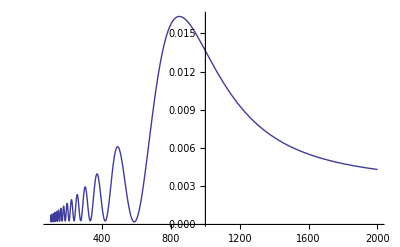

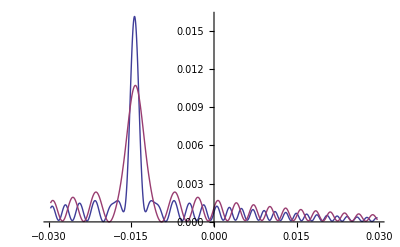

General::stop: Further output of Power will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.` encountered.

General::stop: Further output of Power will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.` encountered.

General::stop: Further output of Power will be suppressed during this calculation.

```mathematica
Plot[Abs[ph[-bf*0.5*(1-q/p),q]^2]/(lambda*(p+q)),{q,100,2000},PlotRange->All,AxesOrigin->{1000,0}] 

Plot[{Abs[ph[x,820]]^2/(lambda*(p+820)),Abs[ph[x,0.25*qfoc]]^2/(lambda*(p+0.25*qfoc))},{x,-bf,bf},PlotRange->All,AxesOrigin->{0,0}] 

(* Plot[Abs[ph[x,0.25*qfoc]]^2/(lambda*(p+0.25*qfoc)),{x,-bf,bf},PlotRange->All,AxesOrigin->{0,0}] *)
```